# 3D Splines Progress

## Most Recent Code--Can’t Return Spline

After we get the basic 3D spline code debugged, we will make it much more structured than it is now and tie it to the rest of the code and all of the track options. However, for testing purposes, we are just using the xPtLst, yPtLst, and zPtLst for the Line button.

```mathematica
xLeftBound=0; 
xRightBound=3000;
yLeftBound=1900;
yRightBound=1000;
```

```mathematica
linePoints3D[]:=
Module[{},
fun[x_]:=Evaluate[Fit[{{xLeftBound,yLeftBound},{xRightBound,yRightBound}},{1,x},x]];
xPtLst={{0,-1000000},{1,xLeftBound},{2,428.57142857},{3,857.143},{4,1285.7},{5,1714.3},{6,2142.86}, {7,xRightBound},{8,1000000}};
yPtLst={{0,1500},{1,yLeftBound},{2,fun[428.57142857]},{3,fun[857.143]},{4,fun[1285.71]},{5,fun[1714.29]},{6,fun[2141.86]},{7,yRightBound},{0,1500}};
zPtLst={{0,1500},{1,1500},{2,1500},{3,1500},{4,1500},{5,1500},{6,1500},{7,1500},{8,1500}};
]
linePoints3D[];
```

```mathematica
Button["Line",linePoints3D[],FrameMargins-> 10]
```

Line

Below is our most recent function for updating the splines. We are having trouble returning the spline function.

```mathematica
updateSpline3D[list_]:=Module[{ptLst=list},
(*Sort the list of points so that the x[k] increase as k increases*)
Clear[x,y,K];
ptLst=N[Sort[ptLst]];
x[k_]:=ptLst[[k,1]];
y[k_]:=ptLst[[k,2]];
K=Length[ptLst]; (*K is equal to 9*)

(*f[k,x] is the cubic we will run from {x[k], y[k]} to {x[k + 1], y[k + 1]}*)
Clear[f,a,b,c,d,k];
f[k_,x_]:=a[k] x^3+b[k] x^2+c[k]x+d[k];


(*Equations for natural cubic spline*)
eqn1=Table[f[k,x[k]]==y[k],{k,1,K-1}];
eqn2=Table[f[k,x[k+1]]==y[k+1],{k,1,K-1}];
(*need derivatives for smoothness at the knots*)
eqn3=Table[(D[f[k,x],x]==D[f[k-1,x],x])/.x-> x[k],{k,2,K-1}];
(*set second derivatives equal to 0 at endpoints*)
eqn4=Table[(D[f[k,x],{x,2}]==D[f[k-1,x],{x,2}])/.x-> x[k],
{k,2,K-1}];
eqn5={(D[f[1,x],{x,2}]/.x->x[1])==0, (D[f[K-1,x],{x,2}]/.x-> x[K])==0};

(*Join all of the equations*)
allEqn=Join[eqn1,eqn2,eqn3,eqn4,eqn5];
(*Solve for coefficients*)
coeffLst=Flatten[Table[{a[k],b[k],c[k],d[k]},{k,K-1}]];
coefs=Chop[Solve[allEqn,coeffLst][[1]]];

(*Substitute the coefficients into the formulas to define the splien function*)
Clear[spline,t,k,thisg];
thisg[k_,t_]:=f[k,t]/.coefs;
Do[With[{m=k,n=k+1},spline[t_]:=thisg[m,t]/;x[m]≤t<x[n]],{k,K-1}];

Return[spline]
]
```

```mathematica
splineXfun=updateSpline3D[xPtLst]
splineYfun=updateSpline3D[yPtLst]
splineZfun=updateSpline3D[zPtLst]
```

spline

Solve::svars: Equations may not give solutions for all "solve" variables.

spline

spline

```mathematica
plotX[y_]=Apply[Function,List[{x},splineXfun]][y]
plotY[y_]=Apply[Function,List[{x},splineYfun]][y]
plotZ[y_]=Apply[Function,List[{x},splineZfun]][y]
ParametricPlot3D[{plotX[k],plotY[k],plotZ[k]},{k,1,10}]
```

spline

spline

spline

-Graphics3D-

## Initial 3D Spline Code--Overrides Each Function

This code has no structure because I just wanted to see what it was doing. I broke it apart and tried to debug the best I could, but found that the each succesive spline was overriding the previous ones. Even though it doesn’t work, I included this code just to show what we have tried.

```mathematica
Button["Line",linePoints3D[],FrameMargins-> 10]
```

Line

```mathematica
zPtLst={{0,1500},{1,1500},{2,1500},{3,1500},{4,1500},{5,1500},{6,1500},{7,1500},{8,1500}};


(*Sort the list of points so that the x[k] increase as k increases*)
Clear[xX,xY,yX,yY,zX,zY,K];
xPtLst=N[Sort[xPtLst]];
xX[k_]:=xPtLst[[k,1]];
xY[k_]:=xPtLst[[k,2]];
K=Length[xPtLst]; (*K is 9 which is the same value for xPtLst, yPtLst, and zPtLst*)

yPtLst=N[Sort[yPtLst]];
yX[k_]:=yPtLst[[k,1]];
yY[k_]:=yPtLst[[k,2]];

zPtLst=N[Sort[zPtLst]];
zX[k_]:=zPtLst[[k,1]];
zY[k_]:=zPtLst[[k,2]];

(*FIRST FUNCTION INFO*)
Clear[firstF,a,b,c,d,k];
firstF[k_,x_]:=a[k] x^3+b[k] x^2+c[k]x+d[k];
firstEqn1=Table[firstF[k,xX[k]]==xY[k],{k,1,K-1}];
firstEqn2=Table[firstF[k,xX[k+1]]==xY[k+1],{k,1,K-1}];
firstEqn3=Table[(D[firstF[k,x],x]==D[firstF[k-1,x],x])/.x-> xX[k],{k,2,K-1}];
(*set second derivatives equal to 0 at endpoints*)
firstEqn4=Table[(D[firstF[k,x],{x,2}]==D[firstF[k-1,x],{x,2}])/.x-> xX[k],
{k,2,K-1}];
firstEqn5={(D[firstF[1,x],{x,2}]/.x->xX[1])==0, (D[firstF[K-1,x],{x,2}]/.x-> xX[K])==0};
firstAllEqn=Join[firstEqn1,firstEqn2,firstEqn3,firstEqn4,firstEqn5];
firstCoeffLst=Flatten[Table[{a[k],b[k],c[k],d[k]},{k,K-1}]];
firstCoefs=Chop[Solve[firstAllEqn,firstCoeffLst][[1]]];
Clear[splineX,t,k,q];
q[k_,t_]:=firstF[k,t]/.firstCoefs;
Do[With[{m=k,n=k+1},splineX[t_]:=q[m,t]/;xX[m]≤t<xX[n]],{k,K-1}];

(*COMMENT THIS OUT WHEN YOU WANT TO TEST!!!*)
(*SECOND FUNCTION INFO*)
Clear[secondF,e,m,n,o,k];
secondF[k_,x_]:=e[k] x^3+m[k] x^2+n[k]x+o[k];
secondEqn1=Table[secondF[k,yX[k]]==yY[k],{k,1,K-1}];
secondEqn2=Table[secondF[k,yX[k+1]]==yY[k+1],{k,1,K-1}];
secondEqn3=Table[(D[secondF[k,x],x]==D[secondF[k-1,x],x])/.x-> yX[k],{k,2,K-1}];
(*set second derivatives equal to 0 at endpoints*)
secondEqn4=Table[(D[secondF[k,x],{x,2}]==D[secondF[k-1,x],{x,2}])/.x-> yX[k],
{k,2,K-1}];
secondEqn5={(D[secondF[1,x],{x,2}]/.x->yX[1])==0, (D[secondF[K-1,x],{x,2}]/.x-> yX[K])==0};
secondAllEqn=Join[secondEqn1,secondEqn2,secondEqn3,secondEqn4,secondEqn5];
secondCoeffLst=Flatten[Table[{e[k],m[k],n[k],o[k]},{k,K-1}]];
secondCoefs=Chop[Solve[secondAllEqn,secondCoeffLst][[1]]];
Clear[splineY,t,k,q];
q[k_,t_]:=secondF[k,t]/.secondCoefs;
Do[With[{m=k,n=k+1},splineY[t_]:=q[m,t]/;yX[m]≤t<yX[n]],{k,K-1}];

(*COMMENT THIS OUT WHEN YOU WANT TO TEST!!!*)
(*THIRD FUNCTION STUFF*)
Clear[thirdF,p,r,s,u,k];
thirdF[k_,x_]:=p[k] x^3+r[k] x^2+s[k]x+u[k];
thirdEqn1=Table[thirdF[k,zX[k]]==zY[k],{k,1,K-1}];
thirdEqn2=Table[thirdF[k,zX[k+1]]==zY[k+1],{k,1,K-1}];
thirdEqn3=Table[(D[thirdF[k,x],x]==D[thirdF[k-1,x],x])/.x-> zX[k],{k,2,K-1}];
(*set second derivatives equal to 0 at endpoints*)
thirdEqn4=Table[(D[thirdF[k,x],{x,2}]==D[thirdF[k-1,x],{x,2}])/.x-> zX[k],
{k,2,K-1}];
thirdEqn5={(D[thirdF[1,x],{x,2}]/.x->zX[1])==0, (D[thirdF[K-1,x],{x,2}]/.x-> zX[K])==0};
thirdAllEqn=Join[thirdEqn1,thirdEqn2,thirdEqn3,thirdEqn4,thirdEqn5];
thirdCoeffLst=Flatten[Table[{p[k],r[k],s[k],u[k]},{k,K-1}]];
thirdCoefs=Chop[Solve[thirdAllEqn,thirdCoeffLst][[1]]];
Clear[splineZ,t,k,q];
q[k_,t_]:=thirdF[k,t]/.thirdCoefs;
Do[With[{m=k,n=k+1},splineZ[t_]:=q[m,t]/;zX[m]≤t<zX[n]],{k,K-1}];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
ParametricPlot3D[{splineX[t],splineY[t],splineZ[t]},{t,1,10}]
```

-Graphics3D-

MAIN PROBLEM: The problem I have noticed is that although it graphs the function above in Parametric Plot (when you remove the splineZ code) and it looks correct, each of splineX, splineY, and splineZ functions below do not correspond to their given points. If you execute as given, you’ll see that all of the plots below correspond what the splineZ function should be. However, if you comment out the code below “THIRD FUNCTION STUFF” above, all three graphs will then model what the splineY function should be (the last function created). Lastly, if you comment out all of the code for the splineY function, all of the graphs show a plot that should be for splineX. I checked my code very carefully, so I am not sure if this is a small error that I missed or something bigger. It seems like it is assigning splineX, splineY, and splineZ to whatever the last function created was.

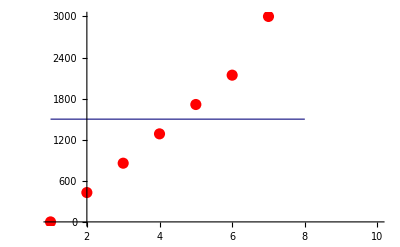

```mathematica
Show[Plot[splineX[t],{t,1,10}], ListPlot[xPtLst,PlotStyle-> Directive[Red,PointSize[0.02]]]]
```

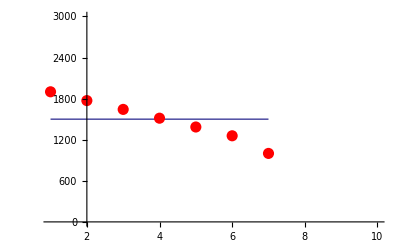

```mathematica
Show[Plot[splineY[t],{t,1,10}], ListPlot[yPtLst,PlotStyle-> Directive[Red,PointSize[0.02]]]]
```

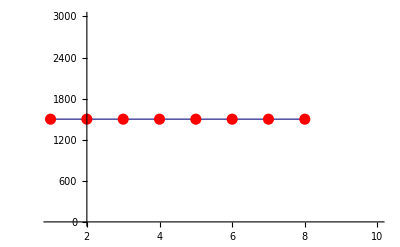

```mathematica
Show[Plot[splineZ[t],{t,1,10}], ListPlot[zPtLst,PlotStyle-> Directive[Red,PointSize[0.02]]]]
```

IMAGES BELOW:

This is what it looks like when the code is executed for splineX with the points. The points seem correct, but the line assigned to splineX is really for splineZ.

-Graphics-

This is what is looks like when you delete the splineZ code and run it again. The graph for splineY is graphed when splineZ and splineX are supposed to be plotted.

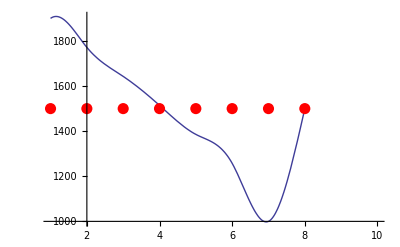

-Graphics-

When you comment out everything except the splineX code, this is the graph for every function.

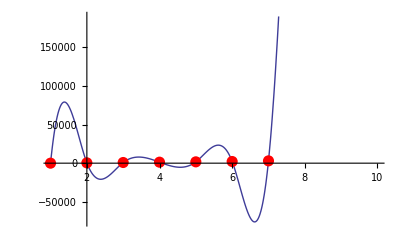

-Graphics-